Expressions for the field components come from Jackson, but the transmission T is given by|E_t/E_0|^2 times a factor involving the angle of incidence and the index of refraction of each material. I’m not sure where this comes from but I found it in the lecture notes here:  https://farside.ph.utexas.edu/teaching/em/lectures/node104.html .

I add the disclaimer that the field expressions here were derived for a dielectric material and are therefore not correct for e.g. dielectric-metal boundaries. The boundary conditions for tangential H and normal D differ from a conductor, because of the way surface charges move around to ensure zero field in the conductor, according to the beginning of chapter 8 in Jackson, so the expressions here are likely at least a little incorrect.

Constants

```mathematica
μ0=4π*10^-7;
ϵ0=8.85*10^-12;
c=1/√(μ0 ϵ0);
angl[z_]:=ArcTan[Im[z]/Re[z]]
```

## vacuum-glass boundary

E field reflected (r) or transmitted (t) relative to incident field E0 for polarization parallel or perpendicular to the plane of incidence, i.e. the plane including the incident, r, and t rays; and boundary between materials with index n1 and n2. Verify for light going from air to glass.

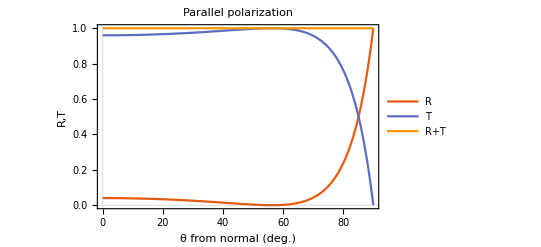

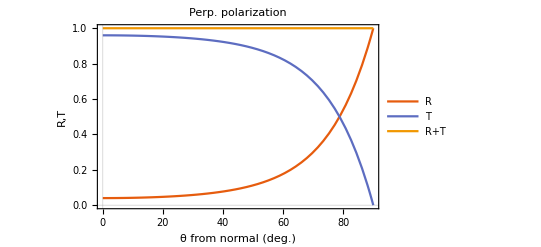

```mathematica
n1=1;
n2=1.5;
μ1=μ0;
μ2=μ0;(*this assumption for μ leads to the familiar Brewster angle of 56 deg., and is usually valid near optical frequencies according to Jackson*)
EtPar=(2n1 n2 Cos[θ])/(μ1/μ2 n2^2 Cos[θ]+n1 √(n2^2-n1^2 Sin[θ]^2));
ErPar=(μ1/μ2 n2^2 Cos[θ]-n1 √(n2^2-n1^2 Sin[θ]^2))/(μ1/μ2 n2^2 Cos[θ]+n1 √(n2^2-n1^2 Sin[θ]^2));
RPar=Abs[ErPar]^2;
TPar=n2/n1 Cos[ArcSin[n1 Sin[θ]/n2]]/Cos[θ] Abs[EtPar]^2;
EtPerp=(2n1 Cos[θ])/(n1 Cos[θ]+μ1/μ2 √(n2^2-n1^2 Sin[θ]^2));
ErPerp=(n1 Cos[θ]-μ1/μ2 √(n2^2-n1^2 Sin[θ]^2))/(n1 Cos[θ]+μ1/μ2 √(n2^2-n1^2 Sin[θ]^2));
RPerp =Abs[ErPerp]^2;
TPerp=n2/n1 Cos[ArcSin[n1 Sin[θ]/n2]]/Cos[θ] Abs[EtPerp]^2;
labels={"R","T","R+T"};
Plot[Evaluate[{RPar,TPar,RPar+TPar}/.θ->deg*π/180],{deg,0,90},PlotLegends->labels,PlotTheme->"Scientific",FrameLabel->{"θ from normal (deg.)","R,T"},PlotLabel->"Parallel polarization"]
Plot[Evaluate[{RPerp,TPerp,RPerp+TPerp}/.θ->deg*π/180],{deg,0,90},PlotLegends->labels,PlotTheme->"Scientific",FrameLabel->{"θ from normal (deg.)","R,T"},PlotLabel->"Perp. polarization"]
```

## vacuum-metal boundary

The reflected field amplitudes (normalized to the incident field amplitude) here come from Fowles modern optics in the chapter Optics of Solids. His rs,p are the reflection amplitudes for polarization perpendicular and parallel to the plane of incidence, respectively. It is assumed that the first medium is vacuum and the second medium has complex index of refraction Ν.

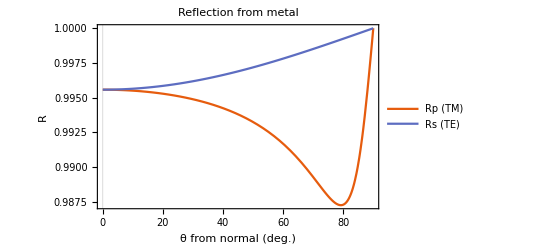

```mathematica
Ν=0.033687+ⅈ 5.4208;(*bulk silver at 780 nm*)
ϕ=ArcSin[Sin[θ]/Ν];
rs=(Cos[θ]-Ν Cos[ϕ])/(Cos[θ]+Ν Cos[ϕ]);
Rs =Abs[rs]^2;
rp=(-Ν Cos[θ]+Cos[ϕ])/(Ν Cos[θ]+Cos[ϕ]);
Rp=Abs[rp]^2;
labels={"Rp (TM)","Rs (TE)"};
Plot[Evaluate[{Rp,Rs}/.θ->deg*π/180],{deg,0,90},PlotLegends->labels,PlotTheme->"Scientific",FrameLabel->{"θ from normal (deg.)","R"},PlotLabel->"Reflection from metal"]
```

```mathematica
Plot[Evaluate[(Rp/Rs)/.θ->deg*π/180],{deg,0,90},PlotLegends->labels,PlotTheme->"Scientific",FrameLabel->{"θ from normal (deg.)","R"},PlotLabel->"Reflection from metal"]
```

```mathematica
rp/.θ->0//angl
```

-2.77676

Phase difference between field components at boundary

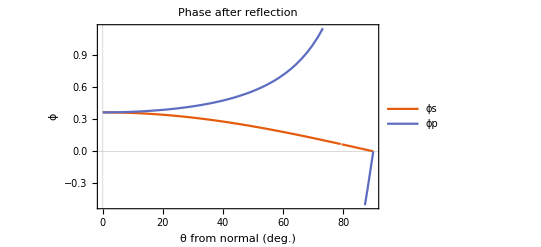

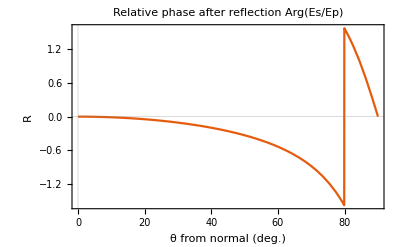

```mathematica
Plot[Evaluate[{rs//angl,rp//angl}/.θ->deg*π/180],{deg,0,90},PlotLegends->{"ϕs","ϕp"},PlotTheme->"Scientific",FrameLabel->{"θ from normal (deg.)","ϕ"},PlotLabel->"Phase after reflection"]
Plot[angl[rs/rp]/.θ->deg*π/180,{deg,0,90},PlotTheme->"Scientific",FrameLabel->{"θ from normal (deg.)","R"},PlotLabel->"Relative phase after reflection Arg(Es/Ep)"]
```

Fidelity to circular polarization incident on a parabolic mirror as a function of angle to the optical axis of the mirror. I assume the reflection stays the same for both components so the fidelity loss is only from differential phase shift on the parallel and perpendicular components.

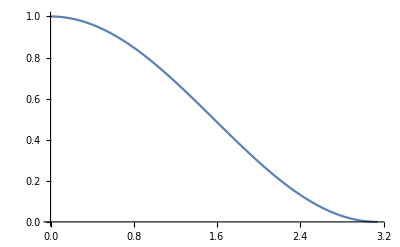

```mathematica
Plot[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{1,ⅇ^(-ⅈ (π/2+α))}]^2,{α,0,π}]
```

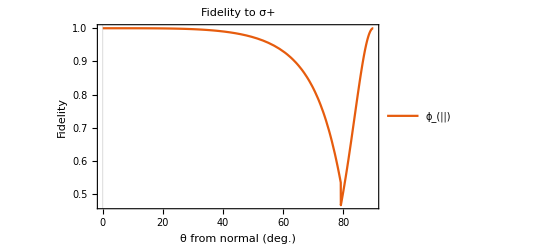

```mathematica
Plot[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{1,ⅇ^(-ⅈ (π/2+α))}]^2/.α->angl[rs/.θ->(deg π)/180]-angl[rp/.θ->(deg π)/180],{deg,0,90},PlotLegends->{"ϕ_(||)","ϕ_⊥"},PlotTheme->"Scientific",FrameLabel->{"θ from normal (deg.)","Fidelity"},PlotLabel->"Fidelity to σ+"]
```

To-do: 
[*] calculate the angle of incidence of a ray hitting the mirror if it is coming from the mirror’s focus at an angle θ wrt to the optical axis. 
[*] do the calculation in terms of z (i.e. the height from the optical axis x) instead of x
[] integrate this overlap over z, multiplying the integrand by the dipole emission pattern for sigma light to get the total fidelity for the distribution of reflected light

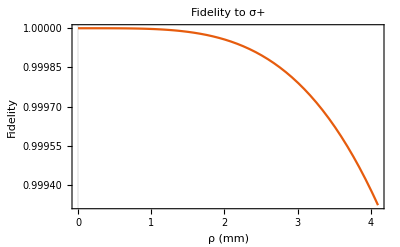

```mathematica
(*parabolic surface with NA ~ 0.6*)
Clear[z]
f=5.26;
zmax=4.1;
x=z^2/(4f);
norm=(ArcTan[D[x,z]]);(*the angle of the surface normal wrt the optical axis*)
Plot[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{1,ⅇ^(-ⅈ (π/2+α))}]^2/.α->angl[rs/.θ->(norm-ArcTan[f-x,z])]-angl[rp/.θ->(norm-ArcTan[f-x,z])],{z,0,zmax},PlotTheme->"Scientific",FrameLabel->{"ρ (mm)","Fidelity"},PlotLabel->"Fidelity to σ+"]
```

consider only the effect of phase:

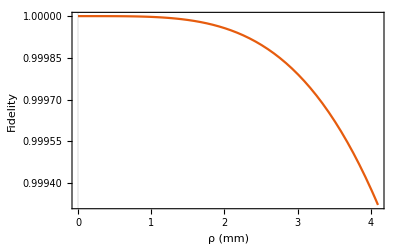

```mathematica
Plot[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{1,ⅇ^(-ⅈ (π/2+α))}]^2/.α->angl[rs/.θ->(norm-ArcTan[f-x,z])]-angl[rp/.θ->(norm-ArcTan[f-x,z])],{z,0,zmax},PlotTheme->"Scientific",FrameLabel->{"ρ (mm)","Fidelity"},LabelStyle->Directive[Black, FontSize->12]]
```

consider the full reflection amplitude for each component

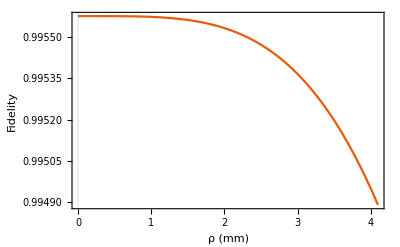

```mathematica
Plot[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{(rp/.θ->(norm-ArcTan[f-x,z]) ), ⅇ^(-ⅈ π/2)rs/.θ->(norm-ArcTan[f-x,z])}]^2,{z,0,zmax},PlotTheme->"Scientific",FrameLabel->{"ρ (mm)","Fidelity"},LabelStyle->Directive[Black, FontSize->12]]
```

Integrate the fidelity over the solid angle, weighted by the emission mode for circular polarization. First, convert the norm expression to a function of the angle from the optical axis

```mathematica
(*ArcTan[D[x,z]]*)
norm=ArcTan[z/(2f)];
```

express z in terms of θ by solving θ=arctan(f-z^2/4f, z):

```mathematica
θmax=ArcTan[f-zmax^2/(4f),zmax];
zmax
2f((-1+√(1+Tan[θ]^2))/Tan[θ])/.θ->θmax
```

4.1

4.1

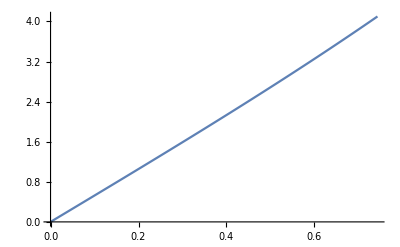

```mathematica
Plot[2f((-1+√(1+Tan[θ]^2))/Tan[θ]),{θ,0,θmax}]
```

Before doing the integral weighted by the emission mode θ dependence, compare the numerical integral result over z with that over θ-- they should be the same.

```mathematica
"z integral"
NIntegrate[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{(rp/.θ->(norm-ArcTan[f-x,z]) ), ⅇ^(-ⅈ π/2)rs/.θ->(norm-ArcTan[f-x,z])}]^2,{z,0,zmax}]/zmax
normθ=ArcTan[Tan[t],-1+√(1+Tan[t]^2)];(*use t as the dummy variable for the θ integral*)
θmax=ArcTan[f-zmax^2/(4f),zmax];
"θ integral"
NIntegrate[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{(rp/.θ->(t/2) ), ⅇ^(-ⅈ π/2)rs/.θ->(t/2)}]^2,{t,0,θmax}]/θmax
```

z integral

0.995433

θ integral

0.99544

Considering the emission probability is larger for smaller θ, it is expected that the loss in fidelity will be less compared to emission which is uniform over θ (which is case above, where no weighting function has been applied)

```mathematica
circPolMode={0,Cos[t],ⅈ}.{0,Cos[t],-ⅈ}
```

1+Cos[t]^2

```mathematica
"σ emission pattern"
emissionWeight=circPolMode;
NIntegrate[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{(rp/.θ->(t/2) ), ⅇ^(-ⅈ π/2)rs/.θ->(t/2)}]^2 emissionWeight,{t,0,θmax}]/(NIntegrate[emissionWeight,{t,0,θmax}])
"unpolarized emission"
emissionWeight=1;
NIntegrate[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{(rp/.θ->(t/2) ), ⅇ^(-ⅈ π/2)rs/.θ->(t/2)}]^2 emissionWeight,{t,0,θmax}]/(NIntegrate[emissionWeight,{t,0,θmax}])
```

σ emission pattern

0.995453+0. ⅈ

unpolarized emission

0.99544

## sag plots and testing

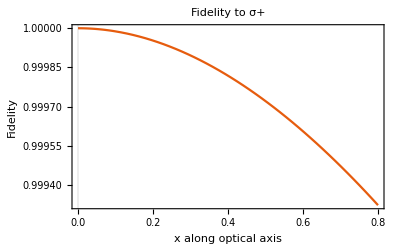

```mathematica
(*parabolic surface with NA ~ 0.6*)
Clear[x]
f=5.26;
xmax=4.1^2/(4f);
(*x=z^2/(4f);*)
z=2 √(f x);
norm=(π/2-ArcTan[D[z,x]]);(*the angle of the surface normal wrt the optical axis x*)
Plot[Abs[1/2{1,ⅇ^(ⅈ π/2)}.{1,ⅇ^(-ⅈ (π/2+α))}]^2/.α->angl[rs/.θ->(norm-ArcTan[f-z^2/(4f),z])]-angl[rp/.θ->(norm-ArcTan[f-z^2/(4f),z])],{x,0,xmax},PlotTheme->"Scientific",FrameLabel->{"x along optical axis","Fidelity"},PlotLabel->"Fidelity to σ+"]
```

angle of surface normal vector is π /2+ arctan(df/dx). Careful with the sign based on the surface concavity.

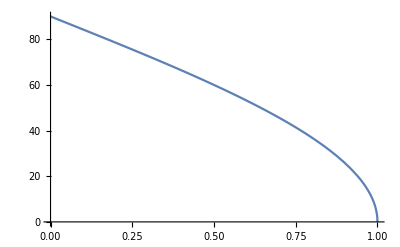

-Graphics-

```mathematica
(*spherical surface*)
R=1;
z=√(R^2-x^2);
norm=180/π(π/2+ArcTan[D[z,x]]);
Plot[norm,{x,0,R}]
(*verify that the angle of the surface normal agrees with the common sense calculation*)
Plot[180/π ArcTan[x,z],{x,0,R}]
```

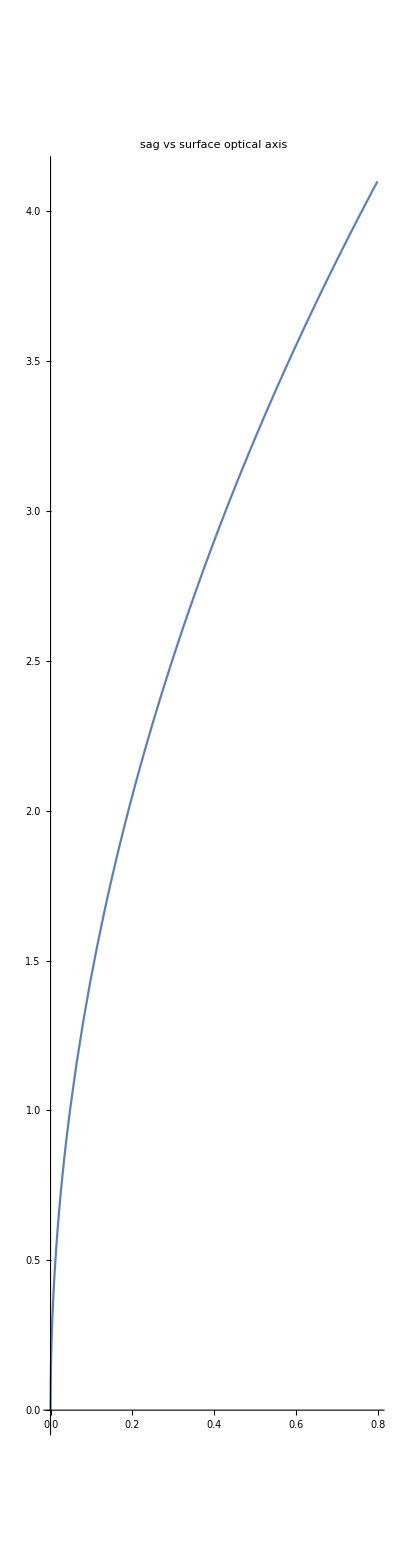

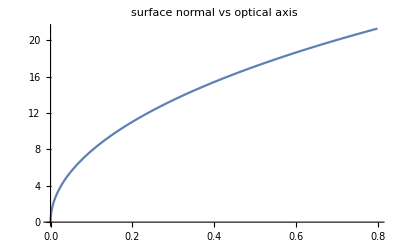

```mathematica
(*parabolic surface*)
f=5.26;
xmax=4.1^2/(4f);
(*x=z^2/(4f);*)
z=2 √(f x);
norm=180/π(π/2-ArcTan[D[z,x]]);
Plot[z,{x,0,xmax},PlotLabel->"sag vs surface optical axis",AspectRatio->(z/.x->xmax)/xmax]
Plot[norm,{x,0,xmax},PlotLabel->"surface normal vs optical axis"]
```

```mathematica
(z/.x->xmax)/xmax
```

5.13171

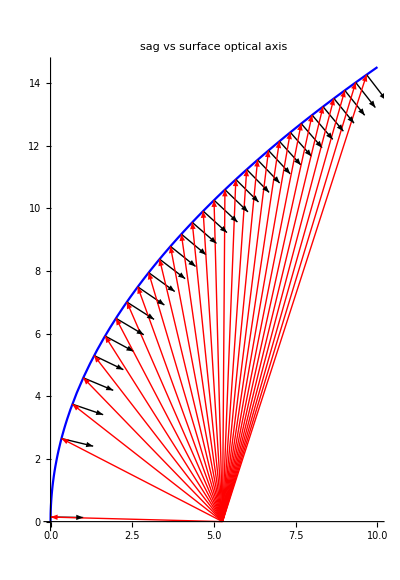

```mathematica
xmax=10;
arrows=30;
Show[Plot[z,{x,0,xmax},PlotLabel->"sag vs surface optical axis",AspectRatio->(z/.x->xmax)/xmax,PlotStyle->Blue],Graphics[Table[Arrow[{{x,z},{x+Cos[π/180 norm],z-Sin[π/180 norm]}}],{x,0.001,xmax,xmax/arrows}]],Graphics[{Red,Table[Arrow[{{f,0},{x,z}}],{x,0.001,xmax,xmax/arrows}]}]]
```

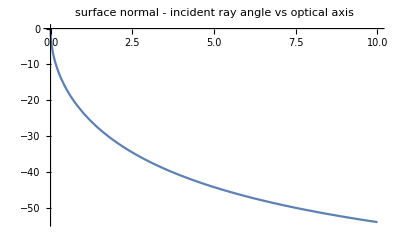

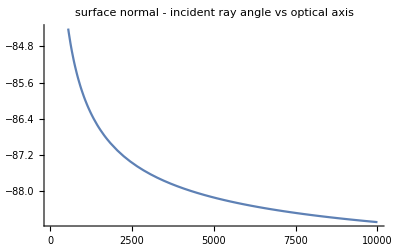

```mathematica
(*the difference between the surface normal angle and incident ray angle, i.e. the angle of incidence on the mirror, should approach 90 deg as the ray strikes a part of the mirror infinitely far away*)
Plot[norm-180/π ArcTan[f-z^2/(4f),z],{x,0,xmax},PlotLabel->"surface normal - incident ray angle vs optical axis"]
Plot[norm-180/π ArcTan[f-z^2/(4f),z],{x,xmax,10000},PlotLabel->"surface normal - incident ray angle vs optical axis"]
```

Plot the sag as a function of cylindrical radius rather than optical axis. x is the optical axis, and z is the radius. the stupid label choice here is because Fowles and/or Jackson took x as the propagation axis.

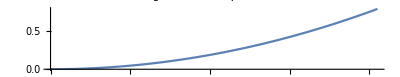

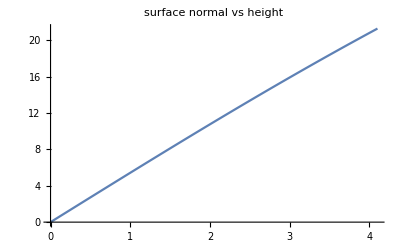

```mathematica
(*parabolic surface*)
f=5.26;
zmax=4.1;
x=z^2/(4f);
norm=180/π(ArcTan[D[x,z]]);
Plot[x,{z,0,zmax},PlotLabel->"sag vs surface optical axis",AspectRatio->(x/.z->zmax)/zmax]
Plot[norm,{z,0,zmax},PlotLabel->"surface normal vs height"]
```

```mathematica
(z/.x->xmax)/xmax
```

5.13171

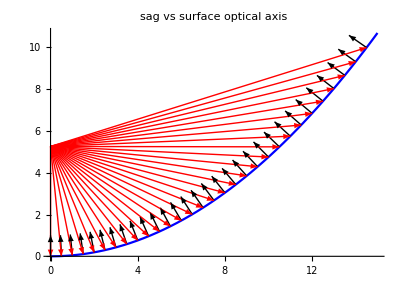

```mathematica
zmax=15;
arrows=30;
Show[Plot[x,{z,0,zmax},PlotLabel->"sag vs surface optical axis",AspectRatio->(x/.z->zmax)/zmax,PlotStyle->Blue],Graphics[Table[Arrow[{{z,x},{z-Sin[π/180 norm],x+Cos[π/180 norm]}}],{z,0.001,zmax,zmax/arrows}]],Graphics[{Red,Table[Arrow[{{0,f},{z,x}}],{z,0.001,zmax,zmax/arrows}]}]]
```

```mathematica
angl[z_]:=ArcTan[Re[z],Im[z]]
```

```mathematica
angl[ⅇ^(-ⅈ π)]
```

π

```mathematica
angl[1+ⅈ]
```

π/4